# (* SubForkNet 4.0 (FreeModel) Sub-cortical Brain Segmentation Copyrights (c) Essam Rashed (essam.rashed@nitech.ac.jp), NITech, Nagoya, JP

```mathematica
(* Experiment Parameters -------------------------------------------------*)
```

```mathematica
NotebookEvaluate["/home/essam/Github/SubForkNet/Notebooks/parameters.nb"];
```

SubForkNet ver.  4.0 (FreeModel)

Direction: [C] Epoches: [100] Batch Size: [4]

Network Architecture: arch0C

```mathematica
(*----------------------LOAD DATA & Preprocessing---------------*)
```

```mathematica
NotebookEvaluate[ReadTrainName];
```

[1/8] Reading MRI...

[2/8] Reading Thalamus...

[3/8] Reading Caudate...

[4/8] Reading Putamen...

[5/8] Reading Pallidum...

[6/8] Reading Hippocampus...

[7/8] Reading Amygdala...

[8/8] Reading Accumbens...

[Done.]

```mathematica
(*----------------------Preparing Data for SubForkNet-------------------*)
```

```mathematica
{a,b,c}=Dimensions[ana];
```

```mathematica
images=Image3DSlices[Image3D[ana]];Clear[ana];
```

```mathematica
shuffledimages=RandomSample@Thread[Range@Length@images->images];
```

```mathematica
keysshuffle=Keys@shuffledimages;
```

```mathematica
mskd1=Lookup[<|Thread[Range@Length@msk1->msk1]|>,keysshuffle];Clear[msk1];
```

```mathematica
mskd2=Lookup[<|Thread[Range@Length@msk2->msk2]|>,keysshuffle];Clear[msk2];
```

```mathematica
mskd3=Lookup[<|Thread[Range@Length@msk3->msk3]|>,keysshuffle];Clear[msk3];
```

```mathematica
mskd4=Lookup[<|Thread[Range@Length@msk4->msk4]|>,keysshuffle];Clear[msk4];
```

```mathematica
mskd5=Lookup[<|Thread[Range@Length@msk5->msk5]|>,keysshuffle];Clear[msk5];
```

```mathematica
mskd6=Lookup[<|Thread[Range@Length@msk6->msk6]|>,keysshuffle];Clear[msk6];
```

```mathematica
mskd7=Lookup[<|Thread[Range@Length@msk7->msk7]|>,keysshuffle];Clear[msk7];
```

```mathematica
MRId=Values@shuffledimages; Clear[shuffledimages];
```

```mathematica
labels1d=ArrayReshape[mskd1,{a,1,b,c}];Clear[mskd1];
```

```mathematica
labels2d=ArrayReshape[mskd2,{a,1,b,c}];Clear[mskd2];
```

```mathematica
labels3d=ArrayReshape[mskd3,{a,1,b,c}];Clear[mskd3];
```

```mathematica
labels4d=ArrayReshape[mskd4,{a,1,b,c}];Clear[mskd4];
```

```mathematica
labels5d=ArrayReshape[mskd5,{a,1,b,c}];Clear[mskd5];
```

```mathematica
labels6d=ArrayReshape[mskd6,{a,1,b,c}];Clear[mskd6];
```

```mathematica
labels7d=ArrayReshape[mskd7,{a,1,b,c}];Clear[mskd7];
```

```mathematica
Dimensions[labels1d]
```

{2560,1,256,256}

```mathematica
(*----------------------Construct Network Modules-------------------------*)
```

```mathematica
NotebookEvaluate[ArchName];  (* N=7 branches architecture *)
```

Network Architecture...

```mathematica
(*----------------------TRAIN NETWORK--------------------------*)
```

```mathematica
logFile=CreateTemporary[]; (* save training data into TMP file *)appendToLog=PutAppend[<|"Batch"->#AbsoluteBatch,"Loss"->#RoundLoss,"VLoss"->#ValidationLoss(*, "Error"->#RoundErrorRate*)|>,logFile]&;TN=NetTrain[SubForkNET,

<|"Input" ->MRId,"Output1"->labels1d,"Output2"->labels2d,"Output3"->labels3d,"Output4"->labels4d,"Output5"->labels5d,"Output6"->labels6d,"Output7"->labels7d|>,
BatchSize->BS,
ValidationSet->Scaled[0.1],
MaxTrainingRounds->Epochs, 
TargetDevice->{"GPU",3}, 
TrainingProgressFunction->appendToLog
 ];
```

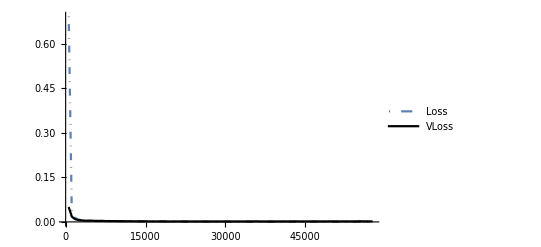

```mathematica
dataset=Dataset[ReadList[logFile]];
LossData=dataset[All,{"Batch","Loss"}];VLossData=dataset[All,{"Batch","VLoss"}];
LossPlot=ListLinePlot[LossData,PlotRange->All,PlotLegends->{"Loss"},PlotStyle->{DotDashed,Thick}];VLossPlot=ListLinePlot[VLossData,PlotRange->All,PlotLegends->{"VLoss"},PlotStyle->{Black}];Show[LossPlot,VLossPlot]
```

```mathematica
dataset[Last]
```

Dataset[<>]

```mathematica
(*------------------------------------------*)
```

```mathematica
Export[NetworkName,TN]; (*NetworkName*)
```

```mathematica
Export[LossName,LossData,"Table"];
```

```mathematica
Export[VLossName,VLossData,"Table"];
```